```mathematica
data={{273 ,2.050},
{273-5 ,2.027},
{273-10 ,2.000},
{273-15 ,1.972},
{273-20 ,1.943},
{273-25 ,1.913},
{273-30 ,1.882},
{273-35 ,1.851},
{273-40 , 1.818},
{273-50 , 1.751},
{273-60 , 1.681},
{273-70 , 1.609},
{273-80 ,1.536},
{273-90, 1.463},
{273-100 ,1.389}}
```

{{273,2.05},{268,2.027},{263,2.},{258,1.972},{253,1.943},{248,1.913},{243,1.882},{238,1.851},{233,1.818},{223,1.751},{213,1.681},{203,1.609},{193,1.536},{183,1.463},{173,1.389}}

```mathematica
FindFormula[data]
```

-1.96293+0.426735 #1^0.4&

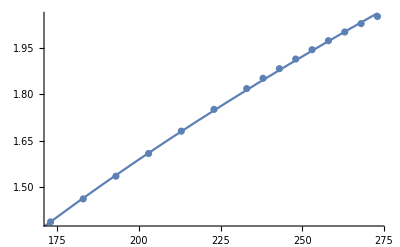

```mathematica
Show[
ListPlot[data],
Plot[-1.9629+0.4267 x^0.4,{x,-173,273}]]
```

```mathematica
Simplify[(-1.9629+0.4267 x^0.4)*18.01528]
```

-35.3622+7.68712 x^0.4

```mathematica
test[q_]:=-35.3622+7.68712 q^0.4;
```

```mathematica
test[273]
```

37.1196

```mathematica
Integrate[test[q]/(265-175),{q,175,265}]
```

31.0119

```mathematica
18*1.875(*kJ/kmolK*)
```

33.75